-Graphics-
-Graphics-

(Bienvenidos a eScience - Estadistica!
https://github.com/josemramirez/mmaescience/statistics -[for Statistical M.])_beta^v14

# Statistical Mechanics - Lec. 7 III. Kinetic Theory of Gases

## III. A General Definitions

(1) -- III. General Definitions

• Kinetic theory explains how the behavior of many tiny particles leads to the properties we see in everyday materials. It uses basic physics equations to connect the motion of individual particles to the characteristics we can measure, like temperature and pressure.

(2) -- Let's talk about thermodynamics and how it relates to the tiny particles that make up everything around us. 

Thermodynamics is all about understanding how big objects behave when they're in balance, using ideas like work, heat, and entropy. We have some rules that tell us how these things change as objects settle into a stable state.

Now, we know that everything is made up of super small particles like atoms and molecules. We have a pretty good idea of how these tiny bits interact and move around. 

So, here's the cool part: if we really understand how these tiny particles behave, we should be able to explain why big objects act the way they do. That's what kinetic theory is all about - trying to connect the dots between the small-scale and large-scale worlds.

Some questions we want to answer are:

```mathematica
(3) -- Let's think about equilibrium in a simple way. Imagine a bunch of particles bouncing around in a box. We say this system is in equilibrium when, on average, nothing seems to change over time. The particles keep moving, but the overall properties of the system stay the same. For example, the temperature, pressure, and density remain constant in different parts of the box. It's like a busy crowd where people are always moving, but the overall distribution of people in the space doesn't change. This steady state is what we call equilibrium for a system of moving particles.
```

```mathematica
(4) -- (2) Most systems in nature tend to move towards equilibrium over time. Think of it like a hot cup of coffee left on a table - it gradually cools down until it reaches room temperature. This is because systems typically evolve to maximize their entropy, a measure of disorder. However, there are exceptions. Some systems, like living organisms, can maintain non-equilibrium states for extended periods by constantly exchanging energy and matter with their surroundings. But even these systems eventually reach equilibrium when they can no longer sustain these exchanges. In general, the Second Law of Thermodynamics tells us that isolated systems will always progress towards equilibrium and maximum entropy.
```

```mathematica
(5) -- Let's explore how a system changes over time when it's not quite in equilibrium. Imagine a cup of hot coffee cooling down in a room. The coffee starts out hotter than its surroundings, so it's not in equilibrium. As time passes, the coffee gradually cools, approaching the room temperature. This process of moving towards equilibrium is what we call the time evolution of a non-equilibrium system. 

We can describe this evolution using statistical mechanics, which looks at the behavior of all the particles in the system. As the system moves towards equilibrium, the distribution of particle energies and positions changes. This change happens in a way that increases the system's entropy, following the Second Law of Thermodynamics.

Understanding this time evolution is crucial for predicting how systems behave and for designing processes in fields like engineering and chemistry.
```

```mathematica
(6) -- Let's start with the simplest system in thermodynamics: the dilute gas. Imagine a box filled with tiny particles, about 100,000,000,000,000,000,000,000 of them! That's a lot, right?

Now, we want to understand how these particles behave as a whole. To do this, we look at each particle's position and momentum at any given moment. Think of it like a giant 3D video game, where we know exactly where each particle is and how fast it's moving.

All these positions and momenta together create what we call a "microstate." It's like a snapshot of the entire system. We can represent this microstate as a single point in a special space called "phase space." This space has six dimensions for each particle (three for position, three for momentum).

As time passes, this point moves around in phase space following specific rules called canonical equations. This movement tells us how the system changes over time.

By studying these microstates and their evolution, we can figure out the big-picture properties of the gas, like its temperature or pressure. This approach is what we call kinetic theory.
```

Statistical Mechanics
Ramirez (7)

```mathematica
MaTeX["\\left\\{\\begin{array}{l}\\frac{\\partial \\vec{q}_{i}}{\\partial t}=\\frac{\\partial \\mathcal{H}}{\\partial \\vec{p}_{i}} \\\\\\frac{\\partial \\vec{p}_{i}}{\\partial t}=-\\frac{\\partial \\mathcal{H}}{\\partial \\vec{q}_{i}}\\end{array}\\right.", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\left\\{\\begin{array}{l}\\frac{\\partial \\vec{q}_{i}}{\\partial t}=\\frac{\\partial \\mathcal{H}}{\\partial \\vec{p}_{i}} \\\\\\frac{\\partial \\vec{p}_{i}}{\\partial t}=-\\frac{\\partial \\mathcal{H}}{\\partial \\vec{q}_{i}}\\end{array}\\right.",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

ToExpression::esntx: Could not parse \left\{\begin{array}{l}\frac{\partial \vec{q}_{i}}{\partial t}=\frac{\partial \mathcal{H}}{\partial \vec{p}_{i}} \\\frac{\partial \vec{p}_{i}}{\partial t}=-\frac{\partial \mathcal{H}}{\partial \vec{q}_{i}}\end{array}\right. as input.

$Failed

(8) -- where the Hamiltonian $\mathcal{H}(\mathbf{p}, \mathbf{q})$, describes the total energy in terms of the set of coordinates $\mathbf{q} \equiv\left\{\vec{q}_{1}, \vec{q}_{2}, \cdots, \vec{q}_{N}\right\}$, and momenta $\mathbf{p} \equiv\left\{\vec{p}_{1}, \vec{p}_{2}, \cdots, \vec{p}_{N}\right\}$. The microscopic equations of motion have time reversal symmetry, i.e. if all the momenta are suddenly reversed, $\mathbf{p} \rightarrow$ $-\mathbf{p}$, at $t=0$, the particles retrace their previous trajectory, $\mathbf{q}(t)=\mathbf{q}(-t)$. This follows from the invariance of $\mathcal{H}$ under the transformation $T(\mathbf{p}, \mathbf{q}) \rightarrow(-\mathbf{p}, \mathbf{q})$.(8) -- Alright, let's break this down into simpler terms:

In thermodynamics, we use something called a Hamiltonian to describe the total energy of a system. This Hamiltonian, which we write as H(p,q), depends on two main things:

1. The positions of all the particles (q)
2. The momenta of all the particles (p)

Now, here's something cool about the equations that describe how these particles move: they work the same way whether time is going forward or backward. This means if we could suddenly reverse the direction of all the particles' momenta, they would retrace their paths exactly. It's like rewinding a movie!

This property is called time reversal symmetry. Mathematically, we can express this by saying that if we change p to -p (reversing all momenta), the Hamiltonian H stays the same.

```mathematica
(9) -- As formulated within thermodynamics, the macrostate $M$, of an ideal gas in equilibrium is described by a small number of state functions such as $E, T, P$, and $N$. The space of macrostates is considerably smaller than the phase space spanned by microstates. Therefore, there must be a very large number of microstates $\mu$ corresponding to the same macrostate $M$.(9) -- In thermodynamics, we describe the overall state of an ideal gas in equilibrium, which we call a macrostate (M), using just a few important quantities. These include energy (E), temperature (T), pressure (P), and the number of particles (N). Think of the macrostate as a big-picture view of the system.

Now, imagine zooming in to see all the individual particles and their positions and velocities. Each unique arrangement of these particles is called a microstate (μ). There are many, many possible microstates for any given macrostate.

The key idea here is that a single macrostate can be achieved by a huge number of different microstates. This is because the macrostate only cares about the overall properties, while microstates represent all the specific ways particles can be arranged to create those properties.
```

```mathematica
(10) -- This many to one correspondence suggests the introduction of a statistical ensemble of microstates. Consider $\mathcal{N}$ copies of a particular macrostate, each described by a different representative point $\mu_{n}(t)$, in the phase space $\Gamma$. Let $d \mathcal{N}(\mathbf{p}, \mathbf{q}, t)$ equal the number of representative points in an infinitesimal volume $d \Gamma=\prod_{i=1}^{N} d^{3} \vec{p}_{i} d^{3} \vec{q}_{i}$ around the point $(\mathbf{p}, \mathbf{q})$. A phase space density $\rho(\mathbf{p}, \mathbf{q}, t)$ is then defined from(10) -- Imagine we have many copies of a system, each in the same overall state but with slightly different arrangements of its particles. We call this collection of copies an "ensemble." 

To understand this better, picture a phase space - a mathematical space where each point represents a possible state of our system. In this space, we have N points, each representing one copy of our system.

Now, let's focus on a tiny volume in this phase space. We count how many of our N points fall within this volume. This count, divided by the size of the volume, gives us the phase space density.

The phase space density tells us how likely we are to find our system in a particular microscopic state, even though its overall (macroscopic) properties remain the same. This concept helps us bridge the gap between the microscopic world of particles and the macroscopic world we observe.
```

Statistical Mechanics
Ramirez (11)

```mathematica
MaTeX["\\rho(\\mathbf{p}, \\mathbf{q}, t) d \\Gamma=\\lim _{\\mathcal{N} \\rightarrow \\infty} \\frac{d \\mathcal{N}(\\mathbf{p}, \\mathbf{q}, t)}{\\mathcal{N}}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\rho(\\mathbf{p}, \\mathbf{q}, t) d \\Gamma=\\lim _{\\mathcal{N} \\rightarrow \\infty} \\frac{d \\mathcal{N}(\\mathbf{p}, \\mathbf{q}, t)}{\\mathcal{N}}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

ρ[p,q,t] d Γ==lim_(N→∞) (d N[p,q,t])/N

(12) -- This quantity can be compared with the objective probability introduced in the previous section. Clearly $\int d \Gamma \rho=1$, and $\rho$ is a properly normalized probability density function in phase space. To compute macroscopic values for various functions $\mathcal{O}(\mathbf{p}, \mathbf{q})$, we shall use the ensemble averages(12) -- Let's break this down into simpler terms:

When we talk about ρ (rho), we're dealing with a special function that describes how likely different states are in our system. It's like a probability map for all possible configurations of particles.

Now, when we integrate ρ over all possible states (that's what ∫ dΓ ρ = 1 means), we always get 1. This tells us that ρ is properly "normalized" - it accounts for all possibilities without leaving anything out or counting anything twice.

To figure out the average values of physical quantities (like energy or momentum), we use what we call "ensemble averages." These are calculated using ρ and the function O(p,q) that represents the quantity we're interested in.

This approach helps us connect the microscopic world of individual particles to the macroscopic properties we can measure in the lab.

Statistical Mechanics
Ramirez (13)

```mathematica
MaTeX["\\langle\\mathcal{O}\\rangle=\\int Gamma \\rho(\\mathbf{p}, \\mathbf{q}, t) \\mathcal{O}(\\mathbf{p}, \\mathbf{q})\\,  d \\", Magnification -> 4]
```

MaTeX::warn: Warning: Input ends in \. Did you forget to use \\ to denote a single backslash?

MaTeX::texerr: Error while running LaTeX.
! File ended while scanning use of \MaTeX.
!  ==> Fatal error occurred, no output PDF file produced!

$Failed

```mathematica
ToExpression[StringReplace["\\langle\\mathcal{O}\\rangle=\\int Gamma \\rho(\\mathbf{p}, \\mathbf{q}, t) \\mathcal{O}(\\mathbf{p}, \\mathbf{q})\\,  d \\",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

$Failed

(14) -- When the exact microstate $\mu$ is specified, the system is said to be in a pure state. On the other hand, when our knowledge of the system is probabilistic, in the sense of its being taken from an ensemble with density $\rho(\Gamma)$, it is said to belong to a mixed state. It is difficult to describe equilibrium in the context of a pure state, since $\mu(t)$ is constantly changing in time according to eqs.(III.1). Equilibrium is more conveniently described for mixed states by examining the time evolution of the phase space density $\rho(t)$, which is governed by the Liouville's equation introduced in the next section.(14) -- Let's break this down in simpler terms:

In thermodynamics, we can describe a system in two ways. First, we have a "pure state," where we know exactly what's happening with every particle. It's like having a perfect snapshot of the system.

The other way is called a "mixed state." Here, we don't know everything precisely, but we have probabilities for different possible arrangements. Imagine shaking a box of marbles - we can't say exactly where each marble is, but we can estimate the chances of finding them in different spots.

Now, when we talk about equilibrium (when things settle down and stop changing), it's tricky to use the pure state idea. That's because the exact positions and speeds of particles are always changing.

Instead, it's easier to think about equilibrium using mixed states. We look at how the probabilities of different arrangements change over time. This is described by something called Liouville's equation, which we'll learn about later.

(15) -- \section*{III.B Liouville's Theorem}
\begin{itemize}
  \item Liouville's Theorem states that the phase space density $\rho(\Gamma, t)$, behaves like an incompressible fluid.
\end{itemize}(15) -- III.B Liouville's Theorem

• Liouville's Theorem tells us that the phase space density ρ(Γ, t) acts like a fluid that can't be squeezed. This means that as the system evolves over time, the density of points in phase space remains constant, just like an incompressible fluid maintains its volume when moved around.

```mathematica
(16) -- Proof: Follow the evolution of $d \mathcal{N}$ pure states in an infinitesimal volume $d \Gamma=$ $\prod_{i=1}^{N} d^{3} \vec{p}_{i} d^{3} \vec{q}_{i}$ around the point $(\mathbf{p}, \mathbf{q})$. According to eqs.(III.1), after an interval $\delta t$ these states have moved to the vicinity of another point $\left(\mathbf{p}^{\prime}, \mathbf{q}^{\prime}\right)$, where(16) -- Let's think about how a group of tiny particles moves in a small space. Imagine we have a bunch of these particles, and we want to track where they go over a short time.

We start by looking at a tiny volume in space, which we call dΓ. This volume is made up of all the possible positions and momenta of our particles. We count how many pure states (specific arrangements of particles) are in this volume, calling this number dN.

Now, we let a little bit of time pass, which we call δt. During this time, our particles move around. They start at a point we call (p,q) and end up near a new point (p',q').

This simple idea helps us understand how particle systems evolve over time, which is crucial in thermodynamics and statistical mechanics. By tracking these movements, we can predict how the system will behave and what properties it will have.
```

Statistical Mechanics
Ramirez (17)

```mathematica
MaTeX["q_{\\alpha}^{\\prime}=q_{\\alpha}+\\dot{q}_{\\alpha} \\delta t+\\mathcal{O}\\left(\\delta t^{2}\\right) \\quad;; \\quad p_{\\alpha}^{\\prime}=p_{\\alpha}+\\dot{p}_{\\alpha} \\delta t+\\mathcal{O}\\left(\\delta t^{2}\\right)", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace[StringSplit["q_{\\alpha}^{\\prime}=q_{\\alpha}+\\dot{q}_{\\alpha} \\delta t+\\mathcal{O}\\left(\\delta t^{2}\\right) \\quad;; \\quad p_{\\alpha}^{\\prime}=p_{\\alpha}+\\dot{p}_{\\alpha} \\delta t+\\mathcal{O}\\left(\\delta t^{2}\\right)", ";;"],{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

{q_α'==q_α+(q̇)_α δ t+O[δ t^2],p_α'==p_α+(ṗ)_α δ t+O[δ t^2]}

```mathematica
(18) -- In the above expression, the $q_{\alpha}$ and $p_{\alpha}$ refer to any of the $6 N$ coordinates and momenta, and $\dot{q}_{\alpha}$ and $\dot{p}_{\alpha}$ are the corresponding velocities. The original volume element $d \Gamma$, is in the shape of a hyper-cube of sides $d p_{\alpha}$ and $d q_{\alpha}$. In the time interval $\delta t$ it gets distorted, and the projected sides of the new volume element are given by(18) -- Let's break this down into simpler terms:

Imagine we're looking at a bunch of particles - say, the atoms in a gas. Each particle has a position and a momentum, which we call q and p. Since we're dealing with many particles (N of them), we need lots of q's and p's to describe them all - 6N in total.

Now, picture a tiny box in this space of q's and p's. As time passes (δt), this box changes shape. It's like the box is flowing along with the particles' motion.

The sides of this box are related to how fast the positions and momenta are changing (that's what we mean by q̇ and ṗ). 

This idea helps us understand how the system of particles evolves over time, which is crucial for studying thermodynamics and statistical mechanics.
```

Statistical Mechanics
Ramirez (19)

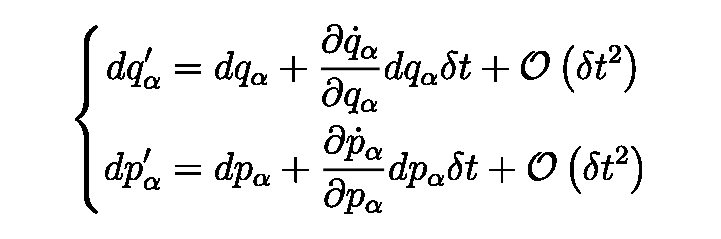

```mathematica
MaTeX["\\left\\{\\begin{aligned}d q_{\\alpha}^{\\prime} & =d q_{\\alpha}+\\frac{\\partial \\dot{q}_{\\alpha}}{\\partial q_{\\alpha}} d q_{\\alpha} \\delta t+\\mathcal{O}\\left(\\delta t^{2}\\right) \\\\d p_{\\alpha}^{\\prime} & =d p_{\\alpha}+\\frac{\\partial \\dot{p}_{\\alpha}}{\\partial p_{\\alpha}} d p_{\\alpha} \\delta t+\\mathcal{O}\\left(\\delta t^{2}\\right)\\end{aligned}\\right.", Magnification -> 4]
```

```mathematica
ToExpression[StringReplace["\\left\\{\\begin{aligned}d q_{\\alpha}^{\\prime} & =d q_{\\alpha}+\\frac{\\partial \\dot{q}_{\\alpha}}{\\partial q_{\\alpha}} d q_{\\alpha} \\delta t+\\mathcal{O}\\left(\\delta t^{2}\\right) \\\\d p_{\\alpha}^{\\prime} & =d p_{\\alpha}+\\frac{\\partial \\dot{p}_{\\alpha}}{\\partial p_{\\alpha}} d p_{\\alpha} \\delta t+\\mathcal{O}\\left(\\delta t^{2}\\right)\\end{aligned}\\right.",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

ToExpression::esntx: Could not parse \left\{\begin{aligned}d q_{\alpha}^{\prime} & =d q_{\alpha}+\frac{\partial \dot{q}_{\alpha}}{\partial q_{\alpha}} d q_{\alpha} \…ac{\partial \dot{p}_{\alpha}}{\partial p_{\alpha}} d p_{\alpha} \delta t+\mathcal{O}\left(\delta t^{2}\right)\end{aligned}\right. as input.

$Failed

```mathematica
(20) -- To order of $\delta t^{2}$, the new volume element is $d \Gamma^{\prime}=\prod_{i=1}^{N} d^{3} \vec{p}_{i}{ }^{\prime} d^{3} \vec{q}_{i}{ }^{\prime}$. From eqs.(III.5) it follows that for each pair of conjugate coordinates(20) -- Let's consider how our system changes over a small time interval. When we look at the new volume element in phase space, we need to account for the slight shifts in both position and momentum for each particle. 

To get a good approximation, we'll include terms up to the second order in time (δt.b2). Our new volume element, which we'll call dΓ', is the product of all these slightly changed position and momentum coordinates for each particle.

This relationship stems from the fundamental equations of motion we discussed earlier. For every pair of position and momentum coordinates (which we call conjugate variables), the transformation preserves the overall volume in phase space. This is a key principle in statistical mechanics, known as Liouville's theorem.
```

Statistical Mechanics
Ramirez (21)

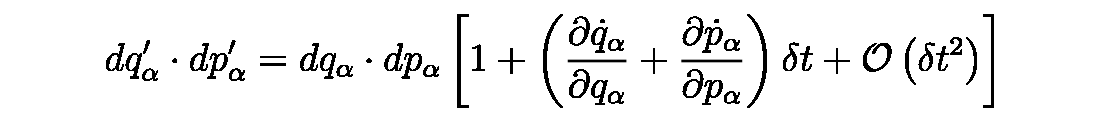

```mathematica
MaTeX["d q_{\\alpha}^{\\prime} \\cdot d p_{\\alpha}^{\\prime}=d q_{\\alpha} \\cdot d p_{\\alpha}\\left[1+\\left(\\frac{\\partial \\dot{q}_{\\alpha}}{\\partial q_{\\alpha}}+\\frac{\\partial \\dot{p}_{\\alpha}}{\\partial p_{\\alpha}}\\right) \\delta t+\\mathcal{O}\\left(\\delta t^{2}\\right)\\right]", Magnification -> 4]
```

```mathematica
ToExpression[StringReplace["d q_{\\alpha}^{\\prime} \\cdot d p_{\\alpha}^{\\prime}=d q_{\\alpha} \\cdot d p_{\\alpha}\\left[1+\\left(\\frac{\\partial \\dot{q}_{\\alpha}}{\\partial q_{\\alpha}}+\\frac{\\partial \\dot{p}_{\\alpha}}{\\partial p_{\\alpha}}\\right) \\delta t+\\mathcal{O}\\left(\\delta t^{2}\\right)\\right]",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

d q_α'·d p_α'==d q_α·d p_α[1+(∂_{q_α} (q̇)_α+∂_{p_α} (ṗ)_α) δ t+O[δ t^2]]

```mathematica
(22) -- But since the time evolution of coordinates and momenta are governed by the canonical eqs.(III.1), we have(22) -- Let's think about how the coordinates and momenta of particles change over time. We know that these changes follow specific rules, which we call the canonical equations. These equations tell us exactly how a particle's position and momentum will evolve as time passes. 

Because of this, we can say that the coordinates and momenta at any future time are completely determined by their initial values. In other words, if we know where a particle starts and how fast it's moving, we can predict its exact path and speed at any point in the future.

This idea is crucial for understanding how systems behave over time and forms the basis for many important concepts in thermodynamics and statistical mechanics.
```

Statistical Mechanics
Ramirez (23)

```mathematica
MaTeX["\\frac{\\partial \\dot{q}_{\\alpha}}{\\partial q_{\\alpha}}=\\frac{\\partial}{\\partial q_{\\alpha}} \\frac{\\partial \\mathcal{H}}{\\partial p_{\\alpha}}=\\frac{\\partial^{2} \\mathcal{H}}{\\partial p_{\\alpha} \\partial q_{\\alpha}};; \\quad \\text {and} \\quad \\frac{\\partial \\dot{p}_{\\alpha}}{\\partial p_{\\alpha}}=\\frac{\\partial}{\\partial p_{\\alpha}}\\left(-\\frac{\\partial \\mathcal{H}}{\\partial q_{\\alpha}}\\right)=-\\frac{\\partial^{2} \\mathcal{H}}{\\partial q_{\\alpha} \\partial p_{\\alpha}}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace[StringSplit["\\frac{\\partial \\dot{q}_{\\alpha}}{\\partial q_{\\alpha}}=\\frac{\\partial}{\\partial q_{\\alpha}} \\frac{\\partial \\mathcal{H}}{\\partial p_{\\alpha}}=\\frac{\\partial^{2} \\mathcal{H}}{\\partial p_{\\alpha} \\partial q_{\\alpha}};; \\quad \\text {and} \\quad \\frac{\\partial \\dot{p}_{\\alpha}}{\\partial p_{\\alpha}}=\\frac{\\partial}{\\partial p_{\\alpha}}\\left(-\\frac{\\partial \\mathcal{H}}{\\partial q_{\\alpha}}\\right)=-\\frac{\\partial^{2} \\mathcal{H}}{\\partial q_{\\alpha} \\partial p_{\\alpha}}", ";;"],{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

ToExpression::esntx: Could not parse \frac{\partial \dot{q}_{\alpha}}{\partial q_{\alpha}}=\frac{\partial}{\partial q_{\alpha}} \frac{\partial \mathcal{H}}{\partial p_{\alpha}}=\frac{\partial^{2} \mathcal{H}}{\partial p_{\alpha} \partial q_{\alpha}} as input.

ToExpression::esntx: Could not parse  \quad \text {and} \quad \frac{\partial \dot{p}_{\alpha}}{\partial p_{\alpha}}=\frac{\partial}{\partial p_{\alpha}}\left(-\frac{\partial \mathcal{H}}{\partial q_{\alpha}}\right)=-\frac{\partial^{2} \mathcal{H}}{\partial q_{\alpha} \partial p_{\alpha}} as input.

{$Failed,$Failed}

```mathematica
(24) -- Thus the projected area in eq.(III.6) is unchanged for any pair of coordinates, and hence the volume element is unaffected, $d \Gamma^{\prime}=d \Gamma$. All the pure states $d \mathcal{N}$, originally in the vicinity of $(\mathbf{p}, \mathbf{q})$ are transported to the neighborhood of $\left(\mathbf{p}^{\prime}, \mathbf{q}^{\prime}\right)$, but occupy exactly the same volume. The ratio $d \mathcal{N} / d \Gamma$ is left unchanged, and $\rho$ behaves like the density of an incompressible fluid.(24) -- Hey there! Let's break this down in a simpler way:

Imagine you have a bunch of particles in a certain space. When these particles move around, they might change their positions and speeds, but the amount of space they occupy stays the same. It's like pouring water from one glass to another - the shape might change, but the volume of water remains constant.

Now, we have a special number called ρ (rho) that tells us how densely packed these particles are in a given space. As the particles move around, this density doesn't change. It's similar to how water density stays the same even when you pour it into different containers.

This behavior is really important in thermodynamics and statistical mechanics because it helps us understand how systems of particles evolve over time without losing or gaining any information about their state.
```

```mathematica
(25) -- The incompressibility condition $\rho\left(\mathbf{p}^{\prime}, \mathbf{q}^{\prime}, t+\delta t\right)=\rho(\mathbf{p}, \mathbf{q}, t)$, can be written in differential form as(25) -- In our study of fluid dynamics, we encounter an important concept known as the incompressibility condition. This condition states that the density of a fluid element remains constant as it moves through space and time. We can express this mathematically as:

ρ(p', q', t + δt) = ρ(p, q, t)

Here, ρ represents the fluid density, p and q are the position coordinates, and t is time. The prime notation indicates the new position after a small time increment δt. This equation tells us that the density at the new position and time is equal to the density at the original position and time.

To make this concept more useful in calculations, we can rewrite it in differential form. This allows us to work with instantaneous rates of change rather than finite differences.
```

Statistical Mechanics
Ramirez (26)

```mathematica
MaTeX["\\frac{d \\rho}{d t}=\\frac{\\partial \\rho}{\\partial t}+\\sum_{\\alpha=1}^{3 N}\\left(\\frac{\\partial \\rho}{\\partial p_{\\alpha}} \\cdot \\frac{d p_{\\alpha}}{d t}+\\frac{\\partial \\rho}{\\partial q_{\\alpha}} \\cdot \\frac{d q_{\\alpha}}{d t}\\right)=0", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\frac{d \\rho}{d t}=\\frac{\\partial \\rho}{\\partial t}+\\sum_{\\alpha=1}^{3 N}\\left(\\frac{\\partial \\rho}{\\partial p_{\\alpha}} \\cdot \\frac{d p_{\\alpha}}{d t}+\\frac{\\partial \\rho}{\\partial q_{\\alpha}} \\cdot \\frac{d q_{\\alpha}}{d t}\\right)=0",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

(d ρ)/dt==∂_{t} ρ+∑_(α=1)^(3 N) (∂_{p_α} ρ·(d p_α)/dt+∂_{q_α} ρ·(d q_α)/dt)==0

```mathematica
(27) -- Note the distinction between $\partial \rho / \partial t$ and $d \rho / d t$ : The former partial derivative refers to the changes in $\rho$ at a particular location in phase space, while the latter total derivative follows the evolution of a volume of fluid as it moves in phase space. Substituting from eq.(III.1) into eq.(III.8) leads to(27) -- Let's break this down in simpler terms:

When we talk about ∂ρ/∂t, we're looking at how the density (ρ) changes over time at one specific point in phase space. It's like watching the traffic at a fixed street corner.

On the other hand, dρ/dt tells us about the density changes as we follow a small volume of fluid moving through phase space. This is more like following a single car as it travels through the city.

These two ways of looking at changes give us different information. When we use the equation from earlier (eq.III.1) in our new equation (eq.III.8), we can see how these different perspectives relate to each other.

Understanding this difference is crucial for grasping how systems evolve in thermodynamics and statistical mechanics.
```

Statistical Mechanics
Ramirez (28)

```mathematica
MaTeX["\\frac{\\partial \\rho}{\\partial t}=\\sum_{\\alpha=1}^{3 N}\\left(\\frac{\\partial \\rho}{\\partial p_{\\alpha}} \\cdot \\frac{\\partial \\mathcal{H}}{\\partial q_{\\alpha}}-\\frac{\\partial \\rho}{\\partial q_{\\alpha}} \\cdot \\frac{\\partial \\mathcal{H}}{\\partial p_{\\alpha}}\\right)=-\\{\\rho;; \\mathcal{H}\\}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace[StringSplit["\\frac{\\partial \\rho}{\\partial t}=\\sum_{\\alpha=1}^{3 N}\\left(\\frac{\\partial \\rho}{\\partial p_{\\alpha}} \\cdot \\frac{\\partial \\mathcal{H}}{\\partial q_{\\alpha}}-\\frac{\\partial \\rho}{\\partial q_{\\alpha}} \\cdot \\frac{\\partial \\mathcal{H}}{\\partial p_{\\alpha}}\\right)=-\\{\\rho;; \\mathcal{H}\\}", ";;"],{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

ToExpression::esntx: Could not parse \frac{\partial \rho}{\partial t}=\sum_{\alpha=1}^{3 N}\left(\frac{\partial \rho}{\partial p_{\alpha}} \cdot \frac{\partial \math…rtial q_{\alpha}}-\frac{\partial \rho}{\partial q_{\alpha}} \cdot \frac{\partial \mathcal{H}}{\partial p_{\alpha}}\right)=-\{\rho as input.

ToExpression::esntx: Could not parse  \mathcal{H}\} as input.

{$Failed,$Failed}

```mathematica
(29) -- where we have introduced the Poisson bracket of two functions in phase space as(29) -- In our exploration of phase space dynamics, we've encountered a powerful tool called the Poisson bracket. This mathematical operation, denoted by {A, B}, allows us to describe the relationship between two functions A and B in phase space. It's defined as:

{A, B} = ∑ᵢ (∂A/∂qᵢ ∂B/∂pᵢ - ∂A/∂pᵢ ∂B/∂qᵢ)

Here, qᵢ and pᵢ represent the generalized coordinates and momenta, respectively. The Poisson bracket helps us understand how these functions evolve over time and interact with each other in the context of a physical system. It's a fundamental concept in classical mechanics and forms the bridge to quantum mechanics through its connection to commutators.
```

Statistical Mechanics
Ramirez (30)

```mathematica
MaTeX["\\{A;; B\\} \\equiv \\sum_{\\alpha=1}^{3 N}\\left(\\frac{\\partial A}{\\partial q_{\\alpha}} \\cdot \\frac{\\partial B}{\\partial p_{\\alpha}}-\\frac{\\partial A}{\\partial p_{\\alpha}} \\cdot \\frac{\\partial B}{\\partial q_{\\alpha}}\\right)=-\\{B;; A\\}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace[StringSplit["\\{A;; B\\} \\equiv \\sum_{\\alpha=1}^{3 N}\\left(\\frac{\\partial A}{\\partial q_{\\alpha}} \\cdot \\frac{\\partial B}{\\partial p_{\\alpha}}-\\frac{\\partial A}{\\partial p_{\\alpha}} \\cdot \\frac{\\partial B}{\\partial q_{\\alpha}}\\right)=-\\{B;; A\\}", ";;"],{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

ToExpression::esntx: Could not parse \{A as input.

ToExpression::esntx: Could not parse  B\} \equiv \sum_{\alpha=1}^{3 N}\left(\frac{\partial A}{\partial q_{\alpha}} \cdot \frac{\partial B}{\partial p_{\alpha}}-\frac{\partial A}{\partial p_{\alpha}} \cdot \frac{\partial B}{\partial q_{\alpha}}\right)=-\{B as input.

ToExpression::esntx: Could not parse  A\} as input.

General::stop: Further output of ToExpression::esntx will be suppressed during this calculation.

{$Failed,$Failed,$Failed}

```mathematica
(31) -- (1) Under the action of time reversal, $(\mathbf{p}, \mathbf{q}, t) \rightarrow(-\mathbf{p}, \mathbf{q},-t)$, the Poisson bracket $\{\rho, \mathcal{H}\}$ changes sign, and eq.(III.9) implies that the density reverses its evolution, i.e. $\rho(\mathbf{p}, \mathbf{q}, t)=$ $\rho(-\mathbf{p}, \mathbf{q},-t)$.(31) -- Let's think about what happens when we reverse time in a physical system. Imagine we could play a movie of particles moving backwards. In this scenario, the positions (q) of the particles would remain the same, but their momenta (p) would flip direction. We represent this as (p, q, t) becoming (-p, q, -t).

Now, there's a special mathematical tool called the Poisson bracket that helps us describe how things change in physics. When we apply time reversal, this Poisson bracket changes sign. 

What does this mean for the density of particles in our system? It means that if we reverse time, the density function behaves in a mirror-like way. Specifically, the density at a given point (p, q) at time t is the same as the density at the point with reversed momentum (-p, q) at the reversed time -t.

This symmetry is a fundamental property of many physical systems and helps us understand their behavior under time reversal.
```

(32) -- (2) The time evolution of the ensemble average in eq.(III.3) is given by (using eq.(III.9))(32) -- Let's break this down into simpler terms:

When we're dealing with a large number of particles, we often look at their average behavior over time. This is what we call the "ensemble average." 

To understand how this average changes as time passes, we use a special equation. This equation helps us predict how the system will behave in the future based on its current state.

The equation we use combines two important concepts:
1. How the system changes naturally over time
2. How external forces or influences affect the system

By putting these together, we can get a clear picture of how the ensemble average evolves. This is really useful for understanding complex systems with many particles, like gases or liquids.

Remember, this is just a simplified way to look at a complex topic. As you learn more, you'll see how these ideas apply to real-world situations in thermodynamics and statistical mechanics.

Statistical Mechanics
Ramirez (33)

```mathematica
MaTeX["\\frac{d\\langle\\mathcal{O}\\rangle}{d t}=\\int d \\Gamma \\frac{\\partial \\rho(\\mathbf{p}, \\mathbf{q}, t)}{\\partial t} \\mathcal{O}(\\mathbf{p}, \\mathbf{q})=\\sum_{\\alpha=1}^{3 N} \\int d \\Gamma \\mathcal{O}(\\mathbf{p}, \\mathbf{q})\\left(\\frac{\\partial \\rho}{\\partial p_{\\alpha}} \\cdot \\frac{\\partial \\mathcal{H}}{\\partial q_{\\alpha}}-\\frac{\\partial \\rho}{\\partial q_{\\alpha}} \\cdot \\frac{\\partial \\mathcal{H}}{\\partial p_{\\alpha}}\\right)", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\frac{d\\langle\\mathcal{O}\\rangle}{d t}=\\int d \\Gamma \\frac{\\partial \\rho(\\mathbf{p}, \\mathbf{q}, t)}{\\partial t} \\mathcal{O}(\\mathbf{p}, \\mathbf{q})=\\sum_{\\alpha=1}^{3 N} \\int d \\Gamma \\mathcal{O}(\\mathbf{p}, \\mathbf{q})\\left(\\frac{\\partial \\rho}{\\partial p_{\\alpha}} \\cdot \\frac{\\partial \\mathcal{H}}{\\partial q_{\\alpha}}-\\frac{\\partial \\rho}{\\partial q_{\\alpha}} \\cdot \\frac{\\partial \\mathcal{H}}{\\partial p_{\\alpha}}\\right)",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

Integrate::nodiffd: ∫dΓ(∂ρ(p,q,t))/(∂t)O(p,q) cannot be interpreted. Integrals are entered in the form ∫fⅆx, ∫_a^b , or ∫_(vars ∈ region) , where ⅆ is entered as EscddEsc.

ToExpression::esntx: Could not parse \frac{d\langle\mathcal{O}\rangle}{d t}=\int d \Gamma \frac{\partial \rho(\mathbf{p}, \mathbf{q}, t)}{\partial t} \mathcal{O}(\ma…{H}}{\partial q_{\alpha}}-\frac{\partial \rho}{\partial q_{\alpha}} \cdot \frac{\partial \mathcal{H}}{\partial p_{\alpha}}\right) as input.

$Failed

```mathematica
(34) -- The partial derivatives of $\rho$ in the above equation can be removed by using the method of integration by parts, i.e. $\int f \rho^{\prime}=-\int \rho f^{\prime}$ since $\rho$ vanishes on the boundaries of the integrations, leading to(34) -- Let's simplify this concept a bit. When we're dealing with the equation we mentioned earlier, we can make it easier to understand by using a technique called integration by parts. This method allows us to get rid of the partial derivatives of ρ (rho).

Here's how it works: ∫f ρ' = -∫ρ f'

This is possible because ρ becomes zero at the edges of where we're integrating. By using this technique, we can transform our original equation into something simpler and more manageable.

Remember, this approach helps us better understand how different parts of our system interact, making it easier to analyze complex thermodynamic situations.
```

Statistical Mechanics
Ramirez (35)

```mathematica
MaTeX["\\begin{aligned}\\frac{d\\langle\\mathcal{O}\\rangle}{d t} & =-\\sum_{\\alpha=1}^{3 N} \\int d \\Gamma \\rho\\left[\\left(\\frac{\\partial \\mathcal{O}}{\\partial p_{\\alpha}} \\cdot \\frac{\\partial \\mathcal{H}}{\\partial q_{\\alpha}}-\\frac{\\partial \\mathcal{O}}{\\partial q_{\\alpha}} \\cdot \\frac{\\partial \\mathcal{H}}{\\partial p_{\\alpha}}\\right)+\\mathcal{O}\\left(\\frac{\\partial^{2} \\mathcal{H}}{\\partial p_{\\alpha} \\partial q_{\\alpha}}-\\frac{\\partial^{2} \\mathcal{H}}{\\partial q_{\\alpha} \\partial p_{\\alpha}}\\right)\\right] \\\\& =-\\int d \\Gamma \\rho\\{\\mathcal{H};; \\mathcal{O}\\}=\\langle\\{\\mathcal{O};; \\mathcal{H}\\}\\rangle\\end{aligned}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace[StringSplit["\\begin{aligned}\\frac{d\\langle\\mathcal{O}\\rangle}{d t} & =-\\sum_{\\alpha=1}^{3 N} \\int d \\Gamma \\rho\\left[\\left(\\frac{\\partial \\mathcal{O}}{\\partial p_{\\alpha}} \\cdot \\frac{\\partial \\mathcal{H}}{\\partial q_{\\alpha}}-\\frac{\\partial \\mathcal{O}}{\\partial q_{\\alpha}} \\cdot \\frac{\\partial \\mathcal{H}}{\\partial p_{\\alpha}}\\right)+\\mathcal{O}\\left(\\frac{\\partial^{2} \\mathcal{H}}{\\partial p_{\\alpha} \\partial q_{\\alpha}}-\\frac{\\partial^{2} \\mathcal{H}}{\\partial q_{\\alpha} \\partial p_{\\alpha}}\\right)\\right] \\\\& =-\\int d \\Gamma \\rho\\{\\mathcal{H};; \\mathcal{O}\\}=\\langle\\{\\mathcal{O};; \\mathcal{H}\\}\\rangle\\end{aligned}", ";;"],{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

ToExpression::esntx: Could not parse  \mathcal{O}\}=\langle\{\mathcal{O} as input.

{$Failed,$Failed,$Failed}

```mathematica
(36) -- Note that the total time derivative cannot be taken inside the integral sign, i.e.(36) -- In thermodynamics, we often deal with integrals that depend on both time and other variables. It's important to understand that we can't simply move the total time derivative inside these integrals. This is because the limits of integration might also change with time.

When we have an integral of the form ∫ f(x,t) dx, where both x and t are changing, we need to be careful. The total time derivative of this integral isn't just the integral of the partial derivative of f with respect to time.

Instead, we need to use the Leibniz rule for differentiation under the integral sign. This rule takes into account both the change in the integrand and the change in the limits of integration over time.

Understanding this concept is crucial for correctly analyzing systems where properties change with time, such as in non-equilibrium thermodynamics or when dealing with moving boundaries in fluid dynamics.
```

Statistical Mechanics
Ramirez (37)

```mathematica
MaTeX["\\frac{d\\langle\\mathcal{O}\\rangle}{d t} \\neq \\int Gamma \\frac{d \\rho(\\mathbf{p}, \\mathbf{q}, t)}{d t} \\mathcal{O}(\\mathbf{p}, \\mathbf{q})\\,  d \\", Magnification -> 4]
```

MaTeX::warn: Warning: Input ends in \. Did you forget to use \\ to denote a single backslash?

MaTeX::texerr: Error while running LaTeX.
! File ended while scanning use of \MaTeX.
!  ==> Fatal error occurred, no output PDF file produced!

$Failed

```mathematica
ToExpression[StringReplace["\\frac{d\\langle\\mathcal{O}\\rangle}{d t} \\neq \\int Gamma \\frac{d \\rho(\\mathbf{p}, \\mathbf{q}, t)}{d t} \\mathcal{O}(\\mathbf{p}, \\mathbf{q})\\,  d \\",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

$Failed

```mathematica
(38) -- This common mistake yields $d\langle\mathcal{O}\rangle / d t=0$ !(38) -- In our study of thermodynamics and statistical mechanics, we often encounter a crucial concept: the time derivative of the average value of an observable. A frequent error is to assume that this quantity, d⟨O⟩/dt, always equals zero. However, this assumption can lead to incorrect conclusions about system dynamics. It's important to carefully consider the time dependence of both the observable and the probability distribution when calculating this derivative.
```

(39) -- (3) If the members of the ensemble correspond to an equilibrium macroscopic state, the ensemble averages must be independent of time. This can be achieved by a stationary density, $\partial \rho_{\text {eq }} / \partial t=0$, i.e. by requiring(39) -- In our study of equilibrium systems, we need to consider a key property: time independence. When we look at a system in equilibrium, its average properties shouldn't change over time. To ensure this, we use a special mathematical tool called the equilibrium density (ρeq). This density needs to remain constant, which we express as ∂ρeq/∂t = 0. By setting up our equations this way, we can accurately describe systems that are stable and unchanging over time, just like the equilibrium states we observe in nature.

Statistical Mechanics
Ramirez (40)

```mathematica
MaTeX["\\left\\{\\rho_{\\mathrm{eq}};; \\mathcal{H}\\right\\}=0", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace[StringSplit["\\left\\{\\rho_{\\mathrm{eq}};; \\mathcal{H}\\right\\}=0", ";;"],{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

ToExpression::esntx: Could not parse \left\{\rho_{\mathrm{eq}} as input.

ToExpression::esntx: Could not parse  \mathcal{H}\right\}=0 as input.

{$Failed,$Failed}

(41) -- A possible solution to the above equation is for $\rho_{\mathrm{eq}}$ to be a function of $\mathcal{H}$, i.e. $\rho_{\mathrm{eq}}(\mathbf{p}, \mathbf{q})=$ $\rho(\mathcal{H}(\mathbf{p}, \mathbf{q}))$. It is then easy to verify that $\{\rho(\mathcal{H}), \mathcal{H}\}=\rho^{\prime}(\mathcal{H})\{\mathcal{H}, \mathcal{H}\}=0$. This solution implies that the value of $\rho$ is constant on surfaces of constant energy $\mathcal{H}$, in phase space. This is indeed the basic assumption of statistical mechanics. For example, in the microcanonical ensemble, the total energy $E$ of an isolated system is specified. All members of the ensemble\\
must then be located on the surface $\mathcal{H}(\mathbf{p}, \mathbf{q})=E$ in phase space. Eq.(III.9) implies that a uniform density of points on this surface is stationary in time. The assumption of statistical mechanics is that the macrostate is indeed represented by such a uniform density of microstates. This is equivalent to replacing the objective measure of probability in eq.(III.2) with a subjective one.(41) -- Let's consider a simpler way to solve our equation. We can make ρ_eq depend on H, which represents the energy of our system. In other words, ρ_eq(p, q) = ρ(H(p, q)). 

This solution means that ρ stays the same on surfaces where the energy H is constant in our phase space. This is actually a fundamental idea in statistical mechanics.

Think about the microcanonical ensemble, where we're dealing with an isolated system with a fixed total energy E. All the possible states of this system must be on the surface where H(p, q) = E in our phase space. Our equation tells us that if we spread points evenly on this surface, they'll stay that way over time.

In statistical mechanics, we assume that this even spread of points (or microstates) represents the macrostate of our system. It's like we're replacing our objective probability with a subjective one based on this assumption.

```mathematica
(42) -- There may be additional conserved quantities associated with the Hamiltonian which satisfy $\left\{L_{n}, \mathcal{H}\right\}=0$. In the presence of such quantities, a stationary density exists for any function of the form $\rho_{\mathrm{eq}}(\mathbf{p}, \mathbf{q})=\rho\left(\mathcal{H}(\mathbf{p}, \mathbf{q}), L_{1}(\mathbf{p}, \mathbf{q}), L_{2}(\mathbf{p}, \mathbf{q}), \cdots\right)$. Clearly, the value of $L_{n}$ is not changed during the evolution of the system, since(42) -- In our study of Hamiltonian systems, we often encounter additional quantities that remain constant during the system's evolution, just like energy. These quantities, which we call conserved quantities, have a special relationship with the Hamiltonian. Mathematically, we express this relationship as {Ln, H} = 0.

When such conserved quantities exist, we can describe the system's equilibrium state using a special function. This function, which we call the stationary density, depends not only on the Hamiltonian H but also on these conserved quantities L1, L2, and so on. We write this as:

ρeq(p, q) = ρ(H(p, q), L1(p, q), L2(p, q), ...)

The values of these conserved quantities Ln don't change as the system evolves over time, which is why they're so useful in describing the system's equilibrium state.
```

Statistical Mechanics
Ramirez (43)

```mathematica
MaTeX["\\begin{aligned}\\frac{d L_{n}(\\mathbf{p}, \\mathbf{q})}{d t} & \\equiv \\frac{L_{n}(\\mathbf{p}(t+d t), \\mathbf{q}(t+d t))-L_{n}(\\mathbf{p}(t), \\mathbf{q}(t))}{d t} \\\\& =\\sum_{\\alpha=1}^{3 N}\\left(\\frac{\\partial L_{n}}{\\partial p_{\\alpha}} \\cdot \\frac{\\partial p_{\\alpha}}{\\partial t}+\\frac{\\partial L_{n}}{\\partial q_{\\alpha}} \\cdot \\frac{\\partial q_{\\alpha}}{\\partial t}\\right) \\\\& =-\\sum_{\\alpha=1}^{3 N}\\left(\\frac{\\partial L_{n}}{\\partial p_{\\alpha}} \\cdot \\frac{\\partial \\mathcal{H}}{\\partial q_{\\alpha}}-\\frac{\\partial L_{n}}{\\partial q_{\\alpha}} \\cdot \\frac{\\partial \\mathcal{H}}{\\partial p_{\\alpha}}\\right)=\\left\\{L_{n}, \\mathcal{H}\\right\\}=0\\end{aligned}", Magnification -> 4]
```

-Graphics-

(44) -- In simpler terms, ρeq depends on certain quantities because all the states that the system can reach, without breaking any conservation laws, have an equal chance of occurring. This is a fundamental principle in statistical mechanics, helping us understand how systems behave at the microscopic level.

(45) -- Alright, let's break this down in simpler terms for an undergraduate:

We've established a formula for the equilibrium state, but we need to understand how systems reach this state. At first glance, this seems impossible due to time reversal symmetry: for every path towards equilibrium, there's a reverse path away from it.

Instead, we focus on showing that systems spend most of their time near equilibrium. This leads us to the concept of ergodicity, which asks whether we can swap time averages for ensemble averages.

When we measure a system's properties, we're looking at just one example from all possible states. Many properties, like pressure, are actually averages over time. Pressure comes from particles hitting container walls, which varies moment to moment.

If our system explores all possible states uniformly over time, we can use ensemble averages instead of time averages. For some systems, we can prove they'll eventually visit all possible states (the ergodic theorem). However, these proofs often involve unrealistically long timescales.

In practice, the mathematical proofs of ergodicity don't quite match up with how real systems behave at equilibrium. We still have more to learn about how microscopic behavior leads to the macroscopic properties we observe.

```mathematica
mathPiXDB1="VarsPaper23_v1.mx";
DumpSave[$WorkDir<>"mathPiXDB/"<>mathPiXDB1,"Global`"];
```

◀ prev - + prox ▶

e Guardar
d Resetear